```mathematica
(* Computer Graphics with Applications of Dr. Makhanov *)
```

```mathematica
(* Lecture 1. Basics of Mathematica 2D Graphics: Parametric Functions. *)
```

```mathematica
SetOptions[{Plot,Plot3D,ParametricPlot,ParametricPlot3D,PolarPlot,Graphics},ImageSize->Small];
(*build in function*)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False]; (* don't shoow execution order*)
```

```mathematica
(* At the Lab replace ImageSize->Small by ImageSize->Medium *)
```

```mathematica
(* The first 2 lines establish the size of the output image and the cell labels.
It is recommended to check the color for the undefined variables. The default color is blue. 
The default error color-Red. Keep these colors. Pay attention! This helps to debug the code.
-Graphics- -Graphics-

 *)
```

```mathematica
(* The delimiters (*  *) are used to enclose comments. Anything that appears between the delimiters is ignored by Mathematica when the cell is evaluated. 
In the lecture notes we additionally use shading to indicate the comments.*)
```

```mathematica
(* In order to see the entire output of the lecture run the Notebook by Evaluation -> Evaluate->NoteBook *)
```

```mathematica
(* Use Shift+Enter to evaluate an individual cell *)
```

```mathematica
(* Important! Type each line of the code in the individual cell *)
```

```mathematica
(*Variables and basic operations
 lhs:=rhs
assigns rhs to be the delayed value of lhs while rhs is maintained in an unevaluated form
When lhs appears it is replaced by rhs evaluated afresh each time.
In other words := waits for the evaluation / delay assignment
As opposed to that = evaluates the assignment immediately, such as 
lhs=rhs
evaluates rhs and assigns the result to be the value of lhs. From then on, lhs is replaced by rhs whenever it appears. 
*)
```

```mathematica
(* Define a variable x equal to 2  using := and = and display it *)
```

```mathematica
x1:=2
```

```mathematica
x1^2+5
```

9

```mathematica
x2=2
```

2

```mathematica
(* Suppress output by ; *)
```

```mathematica
x3=2;
```

```mathematica
x3+1
```

3

```mathematica
(*  Use Shift + Enter to evaluate the cell *)
```

```mathematica
x=5;
```

```mathematica
x^2+1
```

26

```mathematica
(* Define y=1 and evaluate x+y *)
```

```mathematica
y=1;
```

```mathematica
x+y
```

6

```mathematica
(* Variables that are given values retain those values until we quit Mathematica or use Clear. 
Once Clear[] is applied the variable will continue to not have a value until we give it one.
varaible colour change from black to blue*)
```

```mathematica
Clear[x]
```

```mathematica
(* Using the decimal point forces the numerical evaluation.  *)
```

```mathematica
4./5  (*or 4/5. would also works in giving a float num output*)
```

0.8

```mathematica
4/5
```

4/5

```mathematica
Pi (*get pi symbol*)
```

π

```mathematica
Pi * 1. (*get pi value as a floating num*)
```

3.14159

```mathematica
(* Mathematica has a large set of built-in function and libraries. 
When a function is called use [ ]  - around the argument, such as Sin[x]. 
Built-in functions always start with a capital letter such as Cos[x] Abs[x]*)
```

```mathematica
(* A few examples *)
```

```mathematica
Exp[2.]
```

7.38906

```mathematica
Log[7.]
```

1.94591

```mathematica
Sin[Pi/4.]
```

0.707107

```mathematica
Cos[Pi/6.]
```

0.866025

```mathematica
Cos[Pi/6]
```

(√3)/2

```mathematica
(* But *)
```

```mathematica
Cos[Pi/6]
```

(√3)/2

```mathematica
Sin[0.8]
```

0.717356

```mathematica
(*Functions. Pure functions. 2D plots. Parametric functions. Plots of parametric functions   *)
```

```mathematica
(* Defining, calling and plotting functions. 
The standard color scheme highlights the variables by green
 An undefined function or variable is highlighted by blue (very important!)
 *)
```

```mathematica
(* Define f[x] *)
```

```mathematica
f[x_]:=x^2 
(*notice the delay assignment*)
```

```mathematica
(* Note the underscore in the definition f[x_]:=...  -> SYNTAX!!!!*)
```

```mathematica
(* Call f[x] with x=4 *)
```

```mathematica
f[4]
```

16

```mathematica
f[4,2] (*nothing happens *)
```

f[4,2]

```mathematica
(* Plot f[x] for x from -1 to 1
Plot[function, range] 
range -> {variable, start, end(inclusive)}*)
```

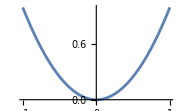

```mathematica
Plot[ f[x],{x,-1,1}]
```

```mathematica
(* A function defined using built-in elementary functions *)
```

```mathematica
f1[x_]:=Sin[x^2]+Cos[x]
```

```mathematica
(* Call f1 *)
```

```mathematica
f1[Pi] (*return the quation of the fundtion given the input value*)
```

-1+Sin[π^2]

```mathematica
(* Plot f1[x], where x ∈ [-14,15] *)
```

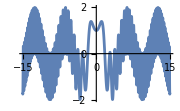

```mathematica
Plot[f1[x],{x,-15,15}]
```

```mathematica
(* Plot a list of functions. f1 defined above and f2[x] is defined by f2[x_]:=Sin[x]+6/(1+x^2)+f1[x]. 
The range of x for f1 and f2 is the same i.e. x∈[-10,15] *)
```

```mathematica
f2[x_]:=Sin[x]+6/(1+x^2)+f1[x]
```

```mathematica
f2[Pi]
```

-1+6/(1+π^2)+Sin[π^2]

```mathematica
(*plotting multiple function : Plot[{functin1[x], function2[x]}, {varible, start, end}]*)
```

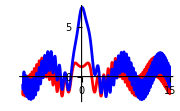

```mathematica
Plot[{f1[x],f2[x]},{x,-10,15},PlotStyle->{Red,Blue}]
```

```mathematica
(* Plot a list of functions using the list of options *)
```

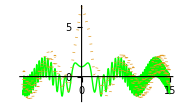

```mathematica
Plot[{f1[x],f2[x]},{x,-10,15},PlotStyle->{{Thick,Green},{Dotted,black}}, Background->White] 
(*f1 with thick green, f2 with doted red*)
```

```mathematica
(* Plot several functions using colors defined by an RGB. Use a color for the background
Include the RGB from the menu: Insert->Color *)
```

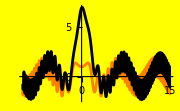

```mathematica
Plot[{f1[x],f2[x]},{x,-10,15},PlotStyle->{RGBColor[1,0.5,0],Black}, Background->Yellow]
```

```mathematica
(* Basics of Lists *)
```

```mathematica
(* Lists generate a collection of objects. As you will see later, 
lists are very important and general structures. They include numbers, functions, matrices, symbolic expressions 
and even images,  graphs and video. 
*)
```

```mathematica
(* A list of numbers (vector)  , comma separated*)
```

```mathematica
A:={1,-5,3.4,9}
```

```mathematica
(* Extract the 4-th element of the list (double [[]]) *)
```

```mathematica
A[[4]]
```

9

```mathematica
(* One can apply the index directly to the list *)
```

```mathematica
(* Matrix *)
```

```mathematica
M1={{1,2,3},{5,6,7}}
```

{{1,2,3},{5,6,7}}

```mathematica
(* Matrix view *)
```

```mathematica
MatrixForm[M1]
```

(1 | 2 | 3
5 | 6 | 7)

```mathematica
M1[[1]]
```

{1,2,3}

```mathematica
(* Extract the element 21 (row=2, col=1) *)
```

```mathematica
M1[[2]][[1]]
```

5

```mathematica
(*  An upcoming  lecture will introduce details of the lists *)
```

```mathematica
(* Functions of 2 or more variables *)
```

```mathematica
f2D[x_,y_]:=x^2+y^2
```

```mathematica
(* Call the function with numerical arguments *)
```

```mathematica
f2D[2,5]
```

29

```mathematica
(* Plot the f2D. The range of x and y must be specified by the lists e.g. {x,-1,1},{y,-1,1} *)
```

```mathematica
Plot3D[f2D[x,y],{x,-1,1},{y,-1,1}] (*plot 3 dimensional graph - built in function*)
```

-Graphics3D-

```mathematica
(* The arguments of the function can be represented by a list. *)
```

```mathematica
f2DL[{x_,y_}]:=x^2+y^2 (*provide list of variable within the argument*)
```

```mathematica
(* Call. Check the difference with f2D  *)
```

```mathematica
f2DL[{2,5,10}] (*do nothing*)
```

f2DL[{2,5,10}]

```mathematica
f2DL[{2,5}]
```

29

```mathematica
ArgL={2,5} (* Define a list as the argument *)
```

{2,5}

```mathematica
f2DL[ArgL]
```

29

```mathematica
Plot3D[f2DL[{x,y}],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* If one or both arguments are symbolic M14 generates a symbolic output  *)
```

```mathematica
Clear[a]
```

```mathematica
f2D[a,5]
```

25+a^2

```mathematica
f2D[1+a^2,Sqrt[1+a+a^2]]
```

1+a+a^2+(1+a^2)^2

```mathematica
(* Note the function "Simplify" -> same identity as the one unsimplify *)
```

```mathematica
Simplify[f2D[1+a^2,Sqrt[1+a+a^2]]]
```

2+a+3 a^2+a^4

```mathematica
(* The arguments can be represented by the general list  a
The advantage is that a can include any number of elements
*)
```

```mathematica
fL[a_]:=a[[1]]^2+a[[2]]^2
```

```mathematica
fL[a_]:=a[[1]]^2+a[[2]]^2 +a[[3]]^2 +a[[4]]^2
```

```mathematica
(* The call and the plot of such a function is similar to f2DL*)
```

```mathematica
fL[{1}]
```

Part::partw: Part 2 of {1} does not exist.

Part::partw: Part 3 of {1} does not exist.

Part::partw: Part 4 of {1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

1+({1}⟦2⟧)^2+({1}⟦3⟧)^2+({1}⟦4⟧)^2

```mathematica
fL[{1,3}]
```

Part::partw: Part 3 of {1,3} does not exist.

Part::partw: Part 4 of {1,3} does not exist.

10+({1,3}⟦3⟧)^2+({1,3}⟦4⟧)^2

```mathematica
fL[{1,3,10}] (*extra argument is disregard -> not included in the equation*)
```

Part::partw: Part 4 of {1,3,10} does not exist.

110+({1,3,10}⟦4⟧)^2

```mathematica
(* Define *)
```

```mathematica
ArgL={1,3}
```

{1,3}

```mathematica
(* Call *)
```

```mathematica
fL[ArgL]
```

Part::partw: Part 3 of {1,3} does not exist.

Part::partw: Part 4 of {1,3} does not exist.

10+({1,3}⟦3⟧)^2+({1,3}⟦4⟧)^2

```mathematica
(* Exceeding the number of arguments is ignored *)
```

```mathematica
fL[{1,3,5}]
```

Part::partw: Part 4 of {1,3,5} does not exist.

35+({1,3,5}⟦4⟧)^2

```mathematica
ArgLExceed={1,3,67}
```

{1,3,67}

```mathematica
fL[ArgLExceed]
```

Part::partw: Part 4 of {1,3,67} does not exist.

4499+({1,3,67}⟦4⟧)^2

```mathematica
(* Generalization:  Transformation f[a_]:=b, where a and b are the lists *)
```

```mathematica
(* Example 1 f:R2->R2 *)
```

```mathematica
fT1[x_,y_]:={x^2+y,Sin[x^2-y]}
```

```mathematica
(* or equivalently  *)
```

```mathematica
fT2[a_]:={a[[1]]^2+a[[2]],Sin[a[[1]]^2-a[[2]]]}
```

```mathematica
(* Call and plot fT1 and fT2  *)
```

```mathematica
fT1[2,7.]
```

{11.,-0.14112}

```mathematica
fT2[{2,7.}] (*passing in a list of number -> index access in equation*)
```

{11.,-0.14112}

```mathematica
(* Functions F:R2->R2 can be displayed by vector fields (see the upcoming lectures). Alternatively the 2 components can be displayed on two independent graphs as follows  *)
```

```mathematica
PL1= Plot3D[fT2[{x,y}][[1]],{x,-1,1},{y,-1,1}] (*plot 2st element of the ft2*)
(*store image in variable -> for combining into a list later*)
```

-Graphics3D-

```mathematica
PL2= Plot3D[fT2[{x,y}][[2]],{x,-1,1},{y,-1,1}](*plot 2nd element of the ft2*)
```

-Graphics3D-

```mathematica
PL={PL1,PL2} (* Combine list of image - notice the curly bracket*)
```

{-Graphics3D-,-Graphics3D-}

```mathematica
(* Any transformation F:R2->Rn or even f:Rm->Rn can be visualized the same way  *)
```

```mathematica
(* Example F:R2->R3, using the list of arguments *)
```

```mathematica
fT3[a_]:={a[[1]]^2+a[[2]],Sin[a[[1]]^2-a[[2]]], a[[1]]^2-a[[2]]^2} (*produce 2 output / graph*)
```

```mathematica
(*plot graph at the same time*)
```

```mathematica
{P1=Plot3D[fT3[{x,y}][[1]],{x,-1,1},{y,-1,1}],
P2=Plot3D[fT3[{x,y}][[2]],{x,-1,1},{y,-1,1}],
P3=Plot3D[fT3[{x,y}][[3]],{x,-1,1},{y,-1,1}]}; (*all graph in a list - suppress with ;*)
```

```mathematica
P123={P1,P2,P3}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Parametric function is a particular case of the transformation f:R->R2 and f:R->R3. 
Its geometric representation is a curve in 2D or 3D - SKIPPPP *)
```

```mathematica
(* Parametric lines in R2 and R3 are familiar objects from the course of LA. (The DA will study them soon) *)
```

```mathematica
(* Define parametric lines in R2 *)
```

```mathematica
(* The direction vector  *)
```

```mathematica
DV={1,2}
```

{1,2}

```mathematica
(* The free term (intercept) *)
```

```mathematica
B={3,3}
```

{3,3}

```mathematica
(* The line equation is given by *)
```

```mathematica
L[t_]:=DV*t+B
```

```mathematica
(* Mathematica outputs the parametric format when we call L[t]*)
```

```mathematica
L[t]
```

{3+t,3+2 t}

```mathematica
(* Note the Matrix(Vector) form *)
```

```mathematica
MatrixForm[L[t]]
```

(3+t
3+2 t)

```mathematica
(* Parametric functions are displayed by ParametricPlot  *)
```

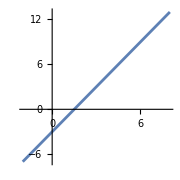

```mathematica
ParametricPlot[L[t],{t,-5,5},AspectRatio->1]
```

```mathematica
(* Define the parametric line as follows *)
```

```mathematica
Lx[t_]:=t+3
```

```mathematica
Ly[t_]:=2t+3
```

```mathematica
Lnew[t_]:={Lx[t],Ly[t]}
```

```mathematica
(* The graph shows the same line *)
```

```mathematica
ParametricPlot[Lnew[t],{t,-5,5},AspectRatio->1]
```

-Graphics-

```mathematica
(* A general (nonlinear) parametric function is defined using the same structure
i.e. the x and the y components of the function are defined separately 
and combined into a 2D vector-function (list)   *)
```

```mathematica
(* A circle with the radius R=3.5 *)
```

```mathematica
R=3.5
```

3.5

```mathematica
xt1[t_]:=R Cos[t] (*x-axis*)
```

```mathematica
yt1[t_]:=R Sin[t] (*y-axis*)
```

```mathematica
(* Define a vector-function *)
```

```mathematica
Cir[t_]:={xt1[t],yt1[t]}
```

```mathematica
(* Plot Cir 1 variable -> 2 output *)
```

```mathematica
(*Plot[] function use linear value of range *)
```

```mathematica
Cir[Pi]
```

{-3.5,0.}

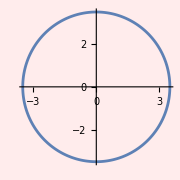

```mathematica
ParametricPlot[Cir[t],{t,0,2 Pi},Background->LightPink] 
(*plot depending on 1 var require 2 args [function, range ]*)
```

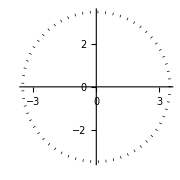

```mathematica
ParametricPlot[Cir[t],{t,0,2 Pi}, PlotStyle->{{Dotted,Black}}, Background->White]
```

```mathematica
(* Spiral - the radius is a decreasing linear function of T 
as angle change, radius keep changing depending on a weighted factor*)
```

```mathematica
RC[t_]:=R(4Pi-t)/(4Pi)
```

```mathematica
RC[0]
```

3.5

```mathematica
RC[2Pi]
```

1.75

```mathematica
xt2[t_]:=RC[t]  Cos[t](*x-axis*)
```

```mathematica
yt2[t_]:=RC[t] Sin[t] (*y-axis*)
```

```mathematica
Spi[t_]:={xt2[t],yt2[t]}
```

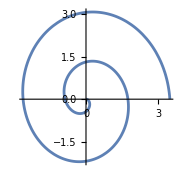

```mathematica
ParametricPlot[Spi[t],{t,0,4Pi},Background->White]
```

```mathematica
(* Plotting two parametric functions, specifying the colors *)
```

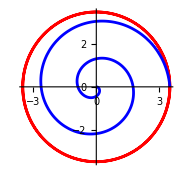

```mathematica
ParametricPlot[{Cir[t],Spi[t]},{t,0,4Pi}, PlotStyle->{Red,Blue}, Background->White]
```

```mathematica
(*control everything at t*)
```

```mathematica
(* Increase the # of rounds of the spiral *)
```

```mathematica
RC1[t_]:=R(4Pi-t)/(4Pi)
```

```mathematica
RC1[0]
```

3.5

```mathematica
RC1[4Pi]
```

0.

```mathematica
xt21[t_]:=RC1[t] Cos[t]
```

```mathematica
yt21[t_]:=RC1[t] Sin[t]
```

```mathematica
Spi1[t_]:={xt21[t],yt21[t]}
```

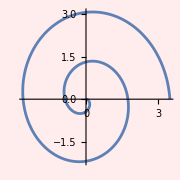

```mathematica
ParametricPlot[Spi1[t],{t,0,4 Pi},Background->LightPink]
```

```mathematica
ParametricPlot[{Cir[t],Spi1[t]},{t,0,4Pi}, PlotStyle->{Red,Blue}]
```

-Graphics-

```mathematica
(* Plotting three parametric functions, specifying the colors and the line type  *)
```

```mathematica
(* The Nephroid curve  *)
```

```mathematica
a=1
```

1

```mathematica
xN[t_]:=a(3Cos[t]-Cos[3t])
```

```mathematica
yN[t_]:=a(3Sin[t]-Sin[3t])
```

```mathematica
Nep[t_]:={xN[t],yN[t]}
```

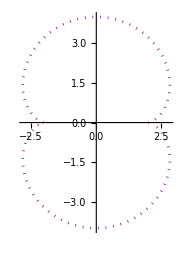

```mathematica
ParametricPlot[Nep[t],{t,0,6}, PlotStyle->{Purple, Dotted}]
```

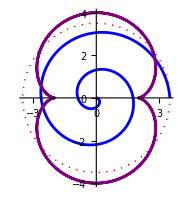

```mathematica
ParametricPlot[{Cir[t],Spi1[t],Nep[t]},{t,0,4Pi}, PlotStyle->{{Thick,Red,Dotted},Blue,Purple}]
```